```mathematica
SetDirectory["~/mthesis/graphanalysis"]
```

/home/remco/Thesis/graphanalysis

```mathematica
data=Import["dep-growth-xulrunner"];
```

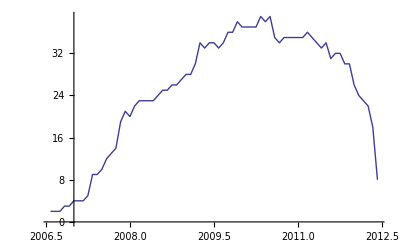

```mathematica
curvepoints=Select[{2000+#⟦1⟧/12,#⟦2⟧}&/@data,#⟦2⟧>0&]⟦1;;-1⟧;
ListLinePlot[curvepoints]
```

```mathematica
Bass[n_,p_,q_,t_]:=n(1-Exp[-(p+q)t])/(1+(q/p)Exp[-(p+q)t])
```

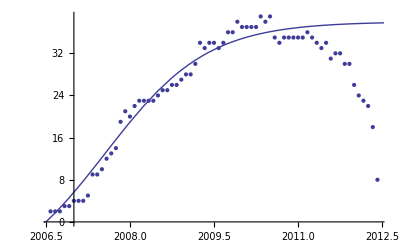

```mathematica
DataPointsPlot=Show[ListPlot[curvepoints],Plot[Max[0,Bass[38,0.26,0.84,t-2006.5]],{t,2000,2013},Frame->True]]
```

```mathematica
nlm=NonlinearModelFit[Take[curvepoints,54],{Bass[M,p,q,t-t0],q>=0,q<=1,p>=0,p<=1},{{t0,2006.5},{M,38},{p,0.26},{q,0.84}},t,MaxIterations->10000];
```

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 10000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.083467, 22.3249, 0.0312548}, is returned.

```mathematica
nlm["BestFit"]
```

(38.0379 (1-ⅇ^(-1.23321 (-2006.56+t))))/(1+4.27611 ⅇ^(-1.23321 (-2006.56+t)))

```mathematica
nlm["ParameterTable"]
```

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
t0 | 2006.56 | 0.112068 | 17904.9 | 7.51591×10^-172
M | 38.0379 | 0.927024 | 41.0323 | 3.60259×10^-40
p | 0.233734 | 0.0646297 | 3.61651 | 0.000694079
q | 0.999472 | 0.216044 | 4.62625 | 0.0000266449

```mathematica
nlm["ANOVATable"]
```

FittedModel::constr: The property values {"ANOVATable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| DF | SS | MS
Model | 4 | 38964.8 | 9741.19
Error | 50 | 167.248 | 3.34497
Uncorrected Total | 54 | 39132. | 
Corrected Total | 53 | 8123.93 |

```mathematica
nlm["ParameterConfidenceIntervalTable", ConfidenceLevel->.95]
```

FittedModel::constr: The property values {"ParameterConfidenceIntervalTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
t0 | 2006.56 | 0.112068 | {2006.33,2006.78}
M | 38.0379 | 0.927024 | {36.1759,39.8999}
p | 0.233734 | 0.0646297 | {0.103922,0.363547}
q | 0.999472 | 0.216044 | {0.565536,1.43341}

```mathematica
nlm["AdjustedRSquared"]
```

0.995384

```mathematica
ConfidenceBands=Table[nlm["SinglePredictionBands",ConfidenceLevel->cl],{cl,{.90,.95,.99,.999}}];
```

FittedModel::constr: The property values {"SinglePredictionBands"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel :: constr will be suppressed during this calculation.

```mathematica
linear[t_]:=(t-2006)*17
```

```mathematica
ConfidenceBandsPlot=Plot[ConfidenceBands,{t,2006,2013},
Filling->{1->{2},3->{4},5->{6},7->{8}},PlotStyle->{None},FillingStyle->{Directive[Red,Opacity[0.1]]}];
```

```mathematica
ModelCurvePlot=Plot[nlm[t],{t,2006,2013},PlotStyle->RGBColor[0.5,0,0]];
```

```mathematica
DataStalksPlot=ListPlot[{curvepoints,{#1,nlm[#1]}&/@curvepoints⟦1;;-1,1⟧},Filling->{1->{2}},PlotStyle->{None,None},FillingStyle->Directive[Black,Opacity[0.2]]];
```

```mathematica
DataDotsPlot1=ListPlot[Take[curvepoints,54],PlotStyle->{Black},FillingStyle->Directive[Black,Opacity[0.2]]];DataDotsPlot2=ListPlot[Take[curvepoints,-17],PlotStyle->{Blue},FillingStyle->Directive[Black,Opacity[0.2]]];
```

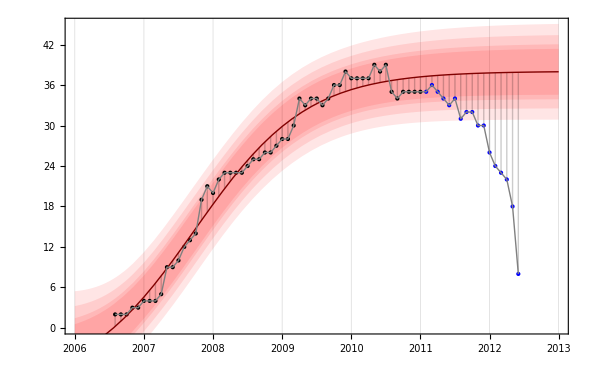

```mathematica
Show[ConfidenceBandsPlot,DataStalksPlot,DataDotsPlot1,DataDotsPlot2,ModelCurvePlot,ListLinePlot[curvepoints,PlotStyle->RGBColor[0.5,0.5,0.5]],PlotRange->{0,45},GridLines->{Automatic,None},GridLinesStyle->Directive[Black,Opacity[0.2]],Frame->True,AxesOrigin->{2006,0}]
```

```mathematica
Export["BassFit-xulrunner-2.pdf",%,ImageSize->600]
```

BassFit-xulrunner-2.pdf

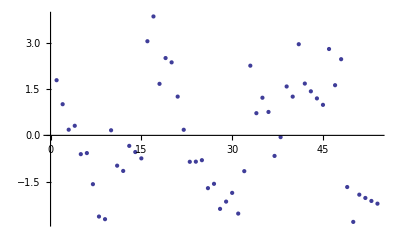

```mathematica
ListPlot[nlm["FitResiduals"]]
```

```mathematica
nlm["FitResiduals"]
```

{448.549,413.669,364.572,360.15,298.295,263.903,224.868,189.091,179.471,131.915,120.333,101.638,-489.246,-330.996,-345.734,-378.954,-500.667,-447.867,-360.538,-328.646,-313.141,-323.958,-460.013,-359.205,-229.416,-125.508,-204.325,-210.695,-193.426,-219.308,-219.117,-86.6109,-21.5331,-25.6134,205.431,288.894,243.079,166.296,137.863,160.1,214.33,158.876,119.058,98.1938,108.594,819.563,635.394,71.3713,56.7652,21.833,320.817,316.943,295.422,247.444,211.185,156.801,85.4293,307.19,287.185,221.498,175.197,142.33,136.932,109.022,83.6044,72.6696,55.1959,7.14941,-3.51438,-80.8499,-106.92,-69.7973,-234.559,-353.29,-408.081,-424.025,-501.222,-523.772,-521.78,-565.352,-582.593,-542.611,-537.515,-459.412,-479.408,-444.609,-349.12,-375.044,-316.481,-298.532,-206.293,-193.859,-192.321,-208.77,-162.293,-99.9731,-67.8928,-83.1309,3.23639,37.1357,108.496,187.25,243.331,377.677,372.228,387.925,380.713,435.54,191.354,190.106,227.751,308.244,356.543,380.607,443.398,511.879,590.015}